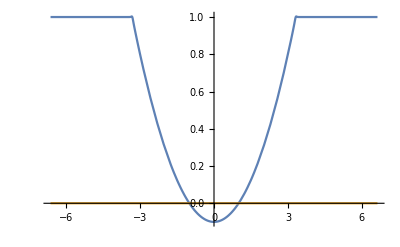

```mathematica
(*Configuration*)
a=0.1;
v=0.0000001;
n=100.;

b=(1.+1./a)^(-n);
Epsilon = Function[x,1.+(a*(x^2.-1.)+ⅈ*v-1.)/(1.+b*x^(2.n))];

X0=2.*Sqrt[1.+1./a];
Plot[{Re[Epsilon[x]],Im[Epsilon[x]]},{x,-X0,X0},PlotRange->Full]

A=1.;
```

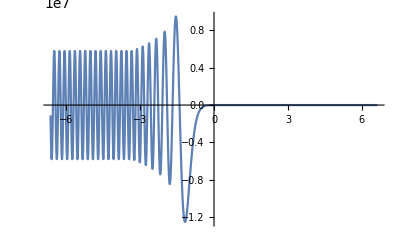

0.0000356109

```mathematica
(*TE-wave*)
ETEEquation={y''[x]+χ^2.*(Epsilon[x]-Sin[θ]^2.)*y[x]==0.};
ETEInitials={y[X0]==A,y'[X0]==ⅈ*χ*A};

ETE=ParametricNDSolveValue[{ETEEquation,ETEInitials},y,{x,-X0,X0},{θ,χ}];
Plot[Re[ETE[0,30.][x]],{x,-X0,X0},PlotRange->Full]

RTE=Function[{θ,χ},Exp[2.*ⅈ*χ*(-X0)]*(ⅈ*χ*ETE[θ,χ][-X0]-ETE[θ,χ]'[-X0])/(ⅈ*χ*ETE[θ,χ][-X0]+ETE[θ,χ]'[-X0])];
TTE=Function[{θ,χ},ETE[θ,χ][X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTE[θ,χ]*Exp[-ⅈ*χ*(-X0)])/ETE[θ,χ][-X0]];

TEDissipation =Function[{θ,χ},1. - Abs[RTE[θ,χ]]^2.-Abs[TTE[θ,χ]]^2.];
TEDissipation[0.,30.]
```

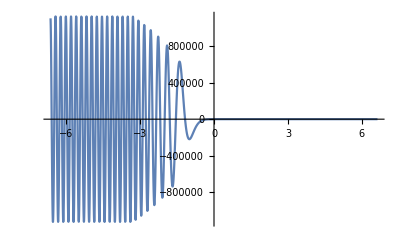

0.0000355848

```mathematica
(*TM-wave*)
BTMEquation={y''[x]-(Epsilon'[x]/Epsilon[x])*y'[x]+χ^2.*(Epsilon[x]-Sin[θ]^2.)*y[x]==0};
BTMInitials={y[X0]==-A,y'[X0]==-ⅈ*χ*Epsilon[X0]*A*Cos[θ]};

BTM=ParametricNDSolveValue[{BTMEquation,BTMInitials},y,{x,-X0,X0},{θ,χ}];
Plot[Re[BTM[0.,30.][x]],{x,-X0,X0},PlotRange->Full]

RTM=Function[{θ,χ},Exp[2.*ⅈ*χ*(-X0)]*(ⅈ*χ*BTM[θ,χ][-X0]-BTM[θ,χ]'[-X0])/(ⅈ*χ*BTM[θ,χ][-X0]+BTM[θ,χ]'[-X0])];
TTM=Function[{θ,χ},BTM[θ,χ][X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTM[θ,χ]*Exp[-ⅈ*χ*(-X0)])/BTM[θ,χ][-X0]];

TMDissipation=Function[{θ,χ},1.-Abs[RTM[θ,χ]]^2.-Abs[TTM[θ,χ]]^2.];
TMDissipation[0.,30.]
```

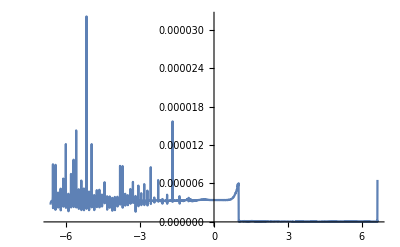

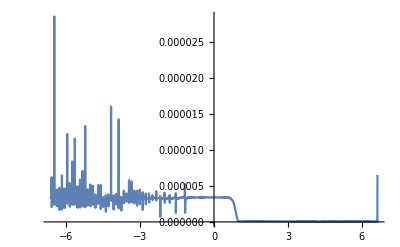

```mathematica
(*Reletive precision*)
values={θ->0.,χ->30.};
ETM=Function[x,ⅈ*BTM[θ,χ]'[x]/(χ*Epsilon[x])];
Plot[Abs[ETE[θ,χ][x]-ETM[x]]/Min[Abs[ETE[θ,χ][x]],Abs[ETM[x]]]/.values,{x,-X0,X0},PlotRange->Full]

BTE=Function[x,(-ⅈ/χ)*ETE[θ,χ]'[x]];
Plot[Abs[BTE[x]+BTM[θ,χ][x]]/Min[Abs[BTE[x]],Abs[BTM[θ,χ][x]]]/.values,{x,-X0,X0},PlotRange->Full]
```

```mathematica
limits={χ1->5.,χ2->50.};
Teta=Function[χ,Abs[θ/.NMaximize[TMDissipation[θ,χ],θ][[2]]]];
Data=Table[Teta[x],{x,χ1/.limits,χ2/.limits}];
```

{m→-0.347467,h→0.424015}

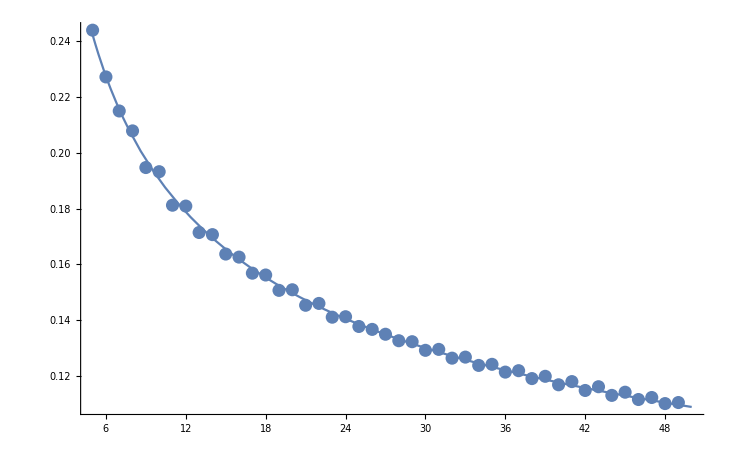

```mathematica
points=Table[Prepend[{Data[[i]]},i+(χ1-1)/.limits],{i,(χ2-χ1)/.limits}];
fit=FindFit[points,h*x^m,{m,h},x]
Experiment=ListPlot[points];
Approximation=Plot[(h*x^m)/.fit,{x,χ1/.limits,χ2/.limits}];
Show[Experiment,Approximation,PlotRange->Automatic]
```